```mathematica
ClearAll["Global`*"]
M:=0.00063
p:=4
μ:=1
ϕini:=0.045514175860860345
ϕend:= 0.659399152881071
tinte =  2.01337*^6;
V[t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[t_]=D[V[t],ϕ[t]];
(*ϕsr,asr*)
sol=NDSolve[{ 3 a'[t]/a[t] ϕ'[t]+Vp[t]==0,
a'[t]==a[t]Sqrt[1/3 (V[t])], 
ϕ[0]==ϕini,a[0]==1},{ϕ,a},
{t,0,tinte}];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
(*ϕ,a*)
Vt[t_]:=M^4 (1-(ϕt[t]/μ)^p)
Vtp[t_]=D[Vt[t],ϕt[t]];
sol1=NDSolve[{ϕt''[t]+ 3 at'[t]/at[t] ϕt'[t]+Vtp[t]==0,
at'[t]==at[t]Sqrt[1/3 (1/2 ϕt'[t]^2+Vt[t])], 
ϕt[0]==ϕsr[0],ϕt'[0]==ϕsrp[0],at[0]==1},{ϕt,at},
{t,0,tinte}];
ϕ[t_]:=(ϕt/.First[sol1])[t]
pϕ[t_]:=(ϕt'/.First[sol1])[t];
ppϕ[t_]:=(ϕt''/.First[sol1])[t];
pppϕ[t_]:=(ϕt'''/.First[sol1])[t];
a[t_]:=(at/.First[sol1])[t];
pa[t_]:=(at'/.First[sol1])[t];
ppa[t_]:=(at''/.First[sol1])[t];
pppa[t_]:=(at'''/.First[sol1])[t];
H[t_]:=pa[t]/a[t]
z[t_]:=(a[t]pϕ[t])/H[t]
tend=t/.FindRoot[ϕ[t]==ϕend,{t,tinte}]; 
Efolds=Log[a[tend]/a[0]];
pH[t_]=D[H[t],t];
z[t_]:=((a[t])^2 pϕ[t])/pa[t];
pz[t_]:=a[t] (pϕ[t] (2-(a[t] ppa[t])/pa[t]^2)+(a[t] ppϕ[t])/pa[t])
ppz[t_]:=2 pa[t] pϕ[t]+(2 a[t]^2 pϕ[t] ppa[t]^2)/pa[t]^3+4 a[t] ppϕ[t]-(a[t]^2 (2 ppa[t] ppϕ[t]+pϕ[t] pppa[t]))/pa[t]^2+(a[t] (-2 pϕ[t] ppa[t]+a[t] pppϕ[t]))/pa[t]
tend
```

InterpolatingFunction::dmval: Input value {2.21471×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.20579×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.32637×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {1.36711×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.36711×10^7

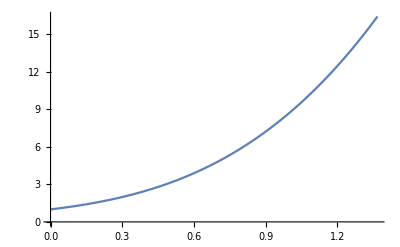

```mathematica
Plot[a[t],{t,0,tend}]
```

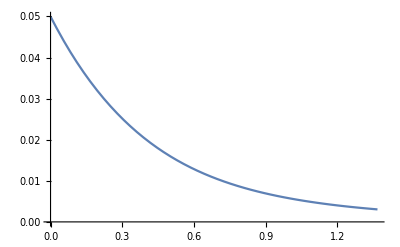

```mathematica
h = 0.05/a[t];
Plot[h,{t,0,tend}]
```

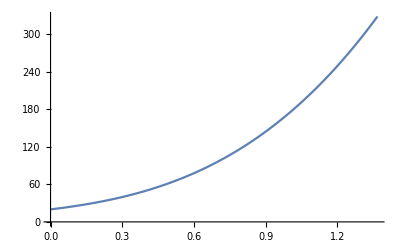

```mathematica
Plot[1/h, {t,0,tend}]
```

```mathematica
(*Calculate phi at the horizon (t=1/H)*)
phiAtHorizon=ϕ[1/h];
```

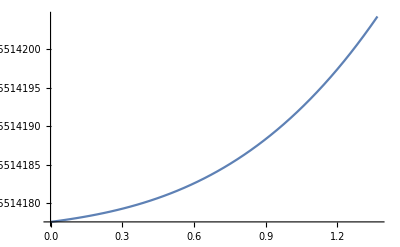

```mathematica
Plot[phiAtHorizon,{t,0,tend}]
```